## Setting

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
Needs["ErrorBarPlots`"];

plotparameters=Evaluate[{Frame->True,BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontColor->Black},LabelStyle->{FontSize->22,FontFamily->"Arial",FontColor->Black}},Axes -> {False, False}, Method->{"OptimizePlotMarkers"->False},FrameStyle->Thickness[0.003]];

SetOptions[Plot,plotparameters];
SetOptions[ListLinePlot,plotparameters];
SetOptions[ListPlot,plotparameters];
SetOptions[ErrorListPlot,plotparameters];
SetOptions[ListContourPlot,plotparameters];
SetOptions[ListLogLogPlot,plotparameters];
SetOptions[ListLogPlot,plotparameters];
SetOptions[Style,SingleLetterItalics->False];
verticalSize=250;
SetDirectory["/media/s8381/HD1/s8381/adaptive_potential/distribution_norm/"];
```

## Parameters and functions

```mathematica
A=1;
σ0=1;
L=15;
τ=0.5;
β=1;
σ1=0.5;
σ2=1.5;
τ1=0.25;
τ2=0.25;
ρ10=1;
ρ1[z_]:=ρ10 Exp[-β A σ0 z];
ρ2[z_]:=ρ20*Exp[(1/2 β A τ z-σ0/τ)^2-σ0^2/τ^2];
ρ3[z_]:=ρ30*(Exp[(1/2 β A τ1 z-σ1/τ1)^2-σ1^2/τ1^2]+Exp[(1/2 β A τ2 z-σ2/τ2)^2-σ2^2/τ2^2]);
p20 = 1/(√(π)*τ);
p2[σ_]:=p20*Exp[-(σ-σ0)^2/τ^2]
p30=1/(√(π)*(τ1+τ2));
p3[σ_]:=p30*(Exp[-(σ-σ1)^2/τ1^2]+Exp[-(σ-σ2)^2/τ2^2])
ϕ[r_,σ_]:=A*σ*r
d=0.4;
Ntot=L/d^3;
```

## Normalization of ρ_2 and ρ_3

```mathematica
area=N[Integrate[ρ1[z],{z,0,L}]]//N
ρ20sol = ρ20/.Solve[Integrate[ρ2[z],{z,0,L}]==area,ρ20][[1]]//N
ρ30sol = ρ30/.Solve[Integrate[ρ3[z],{z,0,L}]==area,ρ30][[1]]//N
```

1.

0.565486

0.325876

```mathematica
(*redefine ρ2 and ρ3 with its normalization factor*)
ρ2New[z_]:=ρ20sol*Exp[(β*A*τ*z/2-σ0/τ)^2-σ0^2/τ^2];
ρ3New[z_]:=ρ30sol*(Exp[(β*A*τ1*z/2-σ1/τ1)^2-σ1^2/τ1^2] + Exp[(β*A*τ2*z/2-σ2/τ2)^2-σ2^2/τ2^2]);
```

```mathematica
NIntegrate[ρ2New[z],{z,0,L}]//N
NIntegrate[ρ3New[z],{z,0,L}]//N
```

1.

1.

## Fig. 1

```mathematica
(*plot ρ1, ρ2 and ρ3 (distribution profile)*)
ρ1plot=ListLinePlot[Table[{z,ρ1[z]},{z,0,L,0.1}],PlotRange->{ Automatic,{0,1.05}},PlotStyle->Blue];
ρ2plot=ListLinePlot[Table[{z,ρ2New[z]},{z,0,L,0.1}],PlotRange->Full,PlotStyle->Red];
ρ3plot=ListLinePlot[Table[{z,ρ3New[z]},{z,0,L,0.1}],PlotRange->Full,PlotStyle-> Green];
fig2aplot = Show[ρ1plot,ρ2plot,ρ3plot,AspectRatio->1,FrameLabel-> {Style["z / σ_0"],Style["ρ_i(z) / ρ_1^0"]},PlotRangePadding->None, Epilog-> Inset[Style["(a)", 30], Offset[{0,0},Scaled[{0.1,0.92}]]]];
```

```mathematica
N2[σ_]:=ρ20sol*p2[σ]*((1-Exp[-β*A*L*σ])/(β*A*σ))
N3[σ_]:=ρ30sol*p3[σ]*((1-Exp[-β*A*L*σ])/(β*A*σ))/(√π*τ1)/p30
p2plot=ListLinePlot[Table[{σ,p2[σ]},{σ,-2,3,0.01}],PlotStyle->Red,PlotRange->{ Automatic,{0,1.2}}];
N2plot=Plot[N2[σ],{σ,-2,3},PlotRange->Automatic];
lineStyle={Thick,Gray,Dashed};
fig2bplot = Show[p2plot,N2plot,AspectRatio-> 1,FrameLabel-> {Style["σ / σ_0"],Style["N(σ) / p_0"]},PlotRangePadding-> None,Epilog-> {Inset[Style["(b)", 30], Offset[{0,0},Scaled[{0.1,0.92}]]],{Directive[lineStyle],Line[{{1,0},{1,2}}]}}];

p3plot=ListLinePlot[Table[{σ,p3[σ] },{σ,-1,3,0.01}],PlotStyle->Green,PlotRange->{ Automatic,{0,2}}];
N3plot=Plot[N3[σ],{σ,-2,3},PlotRange->Full];
lineStyle={Thick,Gray,Dashed};
fig2cplot = Show[p3plot,N3plot,AspectRatio-> 1,FrameLabel-> {Style["σ / σ_0"],Style["N(σ) / p_0"]},PlotRangePadding-> None,Epilog-> {Inset[Style["(c)", 30], Offset[{0,0},Scaled[{0.1,0.92}]]],{Directive[lineStyle],Line[{{1,0},{1,2}}]}}];
```

```mathematica
NIntegrate[N2[σ],{σ,-3,5}]
NIntegrate[N3[σ],{σ,-1,3}]
```

1.

1.

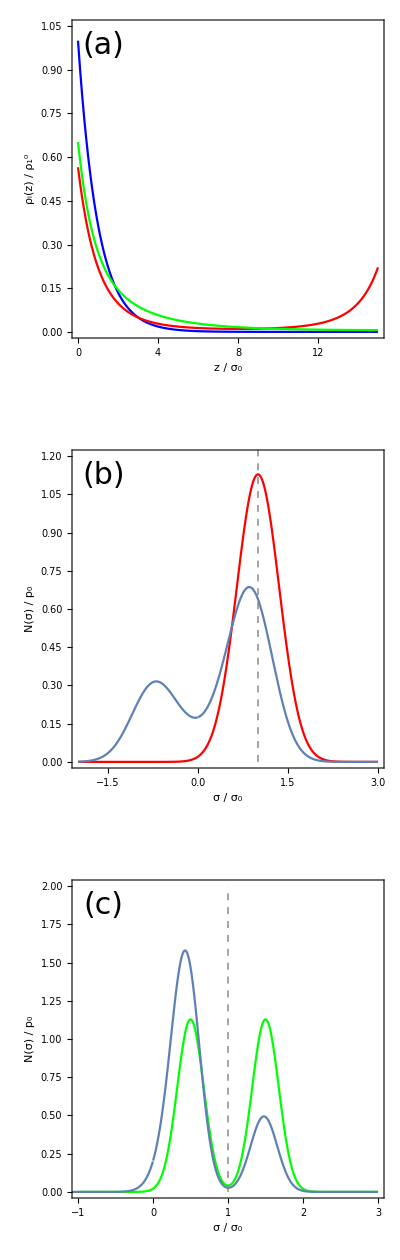

```mathematica
Fig2 = GraphicsGrid[{{fig2aplot},{fig2bplot},{fig2cplot}},ImageSize->400]
```

## Solve σ_2(z) and σ_3(z)

```mathematica
ψ[σ_]:=-β^-1*Log[p3[σ]]
ρrs[r_,σ_]:=q*Exp[-β*ψ[σ]-β*ϕ[r,σ]]
ρr[r_]:=q*Simplify[Integrate[ Exp[-β*ψ[σ]-β*ϕ[r,σ]],{σ,-∞,∞}]]
σ3[r_]:=Integrate[σ*ρrs[r,σ],{σ,-∞,∞}]/ρr[r]
```

```mathematica
σ3Table=Table[{z,σ3[z]},{z,0,15,0.1}]//N;
```

```mathematica
ψ2[σ_]:=-β^-1*Log[p2[σ]]
ρrs2[r_,σ_]:=q*Exp[-β*ψ2[σ]-β*ϕ[r,σ]]
ρr2[r_]:=q*Simplify[Integrate[ Exp[-β*ψ2[σ]-β*ϕ[r,σ]],{σ,-∞,∞}]]
```

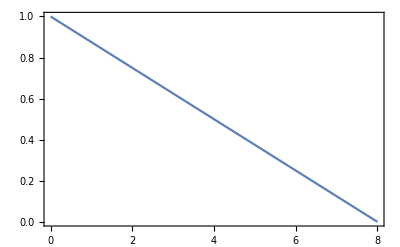

```mathematica
σ2f[r_]:=Integrate[σ*ρrs2[r,σ],{σ,-∞,∞}]/ρr2[r]
σ2Table=Table[{z,σ2f[z]},{z,0,8,1}]//N;
Plot[σ2f[z],{z,0,8}]
```

```mathematica
Simplify[σ2f[z]]
```

(ⅇ^(1. z-0.0625 z^2) (-8.+z) (-0.0183156 (0.125+ⅇ^(0.0625 (-8.+z)^2) (-0.443113+0.0553892 z)+ⅇ^(0.0625 (-8.+z)^2) (0.443113-0.0553892 z) Erf[2.-0.25 z])+1/(-8.+z)^2 0.0183156 (0.125 (8.-1. z)^2-0.0553892 ⅇ^(0.0625 (8.-1. z)^2) (-8.+1. z)^3-0.0553892 ⅇ^(0.0625 (8.-1. z)^2) (-8.+1. z)^3 Erf[2.-0.25 z])))/(-7.08982+0.886227 z+(-7.87128×10^-16+9.8391×10^-17 z) Erf[2.-0.25 z])

```mathematica
Export["s2_z_table.txt",Re[σ2Table]]
Export["s3_z_table.txt",Re[σ3Table]]
```

s2_z_table.txt

s3_z_table.txt